```mathematica
∞
```

```mathematica
z={1,2,4,8};
p[x_,a_]:=Boole[Abs[x]<=a]/(2a)
b=10;
```

```mathematica
Clear[a]
Export["pres_ex_unbouded.pdf",
Plot[Evaluate[Table[p[x,c],{c,z}]],
{x,-b,b},
Filling->Bottom,
PlotLegends->{,,,},
AxesLabel->{"", "pdf"},
PlotRange->{Full,{0,1/(2*z[[1]])+0.1}}
]]
```

pres_ex_unbouded.pdf

```mathematica
p1[x_]:=Boole[Abs[x]<=4]*0.25 (*U[0,4*)
p2[x_]:= 0.5*Exp[-0.5*x]     (*exp(1/2)*)
p3[x_]:=PDF[GammaDistribution[1/2, 4], x] (*Gamma(.5,2)*)
```

```mathematica
Export["pres_mean_2.png",
Plot[{p1[x],p2[x],p3[x]},{x,0,6},
Filling->Bottom,
AxesLabel->{"", "pdf"},
PlotLegends->
{"U[0,4]", "Exp", "Gamma(1/2,4)"},
PlotLabel->"Distributions on  with mean 2"]](*{"U[0,4]", "Exp[1/2]", "Gamma(1/2,2)"} SwatchLegend[1, Range[3], LegendLabel -> "label", 
 LegendFunction -> "Frame"]*)
```

pres_mean_2.png

```mathematica
p1[x_]:=PDF[UniformDistribution[], x]     
p2[x_]:=PDF[BetaDistribution[2,2], x]    
p3[x_]:=PDF[TriangularDistribution[], x] 

Export["example_entropy_01.pdf",
pl = Plot[{p1[x],p2[x],p3[x]},{x,0,1},
Filling->Bottom,
AxesLabel->{"", "pdf"},
PlotLegends->
{Style["U[0,1]",18], Style["Beta(2,2)",18], Style["Triangular",18]},
BaseStyle -> FontSize -> 14,
TicksStyle -> Larger,
PlotLabel->Style["Continuous densities on [0,1]",20]]]
```

example_entropy_01.pdf

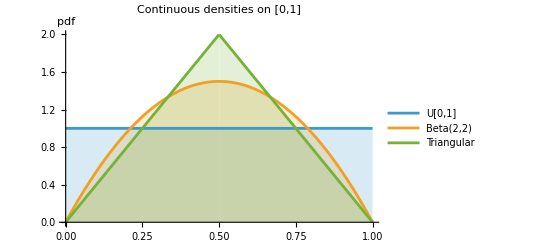

```mathematica
Framed[LineLegend[{Red,Green,Blue},{"red","green","blue"},LabelStyle->10,LegendMarkerSize->5,LegendMargins->0]]
```

```mathematica
ColorData[116,"ColorList"][[1,3]]
```

0.8

```mathematica
Export[".png"] TicksStyle -> Larger,□
```